```mathematica
ClearAll["Global`*"]
```

```mathematica
xdata=Table[i,{i,-1,10,1}];
```

```mathematica
f1[x_]:=If[Im[w1*x^2+w2*x+w3]==0,w1*x^2+w2*x+w3,10^11];
```

```mathematica
ydata=Map[f1,xdata]/.{w1->1,w2->2,w3->3};
ydataAdjusted=Table[ydata[[i]]+RandomReal[{-15,15}],{i,1,Length[ydata]}];
```

```mathematica
combodata[x_,y_]:=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
c1=combodata[xdata,ydata];
c2=combodata[xdata,ydataAdjusted];
```

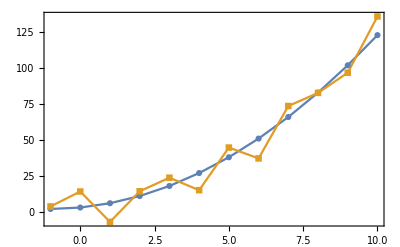

```mathematica
ListPlot[{c1,c2},Joined->{True, True},PlotMarkers->Automatic,Frame->True,Axes->False]
```

```mathematica
nlm=NonlinearModelFit[c2,f1[x],{w1,w2,w3},x];
params=nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
w1 | 1.29358 | 0.266137 | 4.86058 | 0.000895111
w2 | -0.474217 | 2.52947 | -0.187477 | 0.855445
w3 | 5.13086 | 5.11695 | 1.00272 | 0.342193

```mathematica
unpack[pars_]:=Table[params[[1,1,i]][[2]],{i,2,4,1}];
pset=unpack[params];
```

```mathematica
f1[10]/.{w1->pset[[1]],w2->pset[[2]],w3->pset[[3]]}
```

129.747